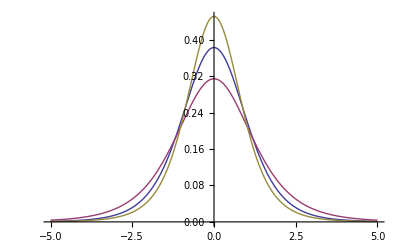

```mathematica
(*  Exact density of the Student two-sample t-statistic for odd sample sizes Subscript[n, 1]=2m+1 and Subscript[n, 2]=2k+1.
Sample variances are Subscript[σ, 1]^2 and Subscript[σ, 2]^2, Subscript[σ, 1]^2≠Subscript[σ, 2]^2. Ray and Pitman (1961)              *)
 
ExactTSTPDF[m_,k_,σ1_,σ2_,u_]:=Module[ {a,b,σ,α,β},
  
                    Subscript[σ, 1]:=σ1;                                                                                Subscript[σ, 2]:=σ2;

a:=(Subscript[σ, 1]^2(1/(2m+1)+1/(2k+1))/(2m+2k))/(Subscript[σ, 1]^2/(2m+1)+Subscript[σ, 2]^2/(2k+1));                             b:=(Subscript[σ, 2]^2(1/(2m+1)+1/(2k+1))/(2m+2k))/(Subscript[σ, 1]^2/(2m+1)+Subscript[σ, 2]^2/(2k+1));

α[r_]:=((-1)^(m-r-1)(1/(2b)-1/(2a))^r Binomial[m+n-r-2, m-r-1])/((2a)^m(2b)^k(1/(2b)-1/(2a))^(m+k-1)r!);       β[r_]:=((-1)^(k-r-1)(1/(2a)-1/(2b))^r Binomial[m+n-r-2, n-r-1])/((2a)^m(2b)^k(1/(2a)-1/(2b))^(m+k-1)r!);

(2π)^(-1/2)(∑_(r=0)^(m-1) (α[r]Gamma[r+3/2](1/(2a)+u^2/2)^(-(r+3/2)))+∑_(r=0)^(k-1) (β[r]Gamma[r+3/2](1/(2b)+u^2/2)^(-(r+3/2))))
];


Plot[{ExactTSTPDF[1,2,1   ,1.001    ,x],
        ExactTSTPDF[1,2,1   ,0.5,x],
        ExactTSTPDF[1,2,0.5,1   ,x]},{x,-5,5}]
```

```mathematica
(* Constant Subscript[K, g] for the asymptotic approximation to the Student two-sample t-statistic. 
Zholud D.S. (2013)                                                  *)

KgTST[n1_,n2_,σ1_,σ2_]:=Module[ {n,a,b,σ,α,β,w},

		Subscript[n, 1]=n1;                             Subscript[n, 2]=n2;
		Subscript[σ, 1]=σ1;                             Subscript[σ, 2]=σ2;
		α= (Subscript[n, 1]-1)/(Subscript[n, 1]+Subscript[n, 2]-2)(1/Subscript[n, 1]+1/Subscript[n, 2]);                             β= (Subscript[n, 2]-1)/(Subscript[n, 1]+Subscript[n, 2]-2)(1/Subscript[n, 1]+1/Subscript[n, 2]);
		    Subscript[w, 0]=ArcCos[√(Subscript[n, 2]/(Subscript[n, 1]+Subscript[n, 2]))];
(((Subscript[n, 1]-1)/α)^((Subscript[n, 1]-1)/2)((Subscript[n, 2]-1)/β)^((Subscript[n, 2]-1)/2)(1/Subscript[n, 1]+1/Subscript[n, 2])^((Subscript[n, 1]+Subscript[n, 2]-2)/2))/(Subscript[n, 1]+Subscript[n, 2]-2)^((Subscript[n, 1]+Subscript[n, 2]-2)/2)×Gamma[(Subscript[n, 1]+Subscript[n, 2])/2]/(Gamma[(Subscript[n, 1]+Subscript[n, 2]-1)/2] √π Subscript[σ, 1]^Subscript[n, 1] Subscript[σ, 2]^Subscript[n, 2])
		×NIntegrate[Cos[x]^(Subscript[n, 1]+Subscript[n, 2]-2)/((Cos[x-Subscript[w, 0]]^2/Subscript[σ, 1]^2+Sin[x-Subscript[w, 0]]^2/Subscript[σ, 2]^2)^((Subscript[n, 1]+Subscript[n, 2])/2)),{x,-π/2,π/2}]
]
```

```mathematica
(* Asymptotic expansion for the density of the Student two-sample t-statistic, Subscript[n, 1]=3, Subscript[n, 2]=5, Subscript[σ, 1]^2/Subscript[σ, 2]^2=0.5 *)

FullSimplify[Series[ExactTSTPDF[1,2,1,√2,x],{x,∞,10}]] //TraditionalForm
```

539055/(4096 x^7)-41507235/(16384 x^9)+O((1/x)^11)

```mathematica
(* Asymptotic expansion for the asymptotic approximation of Zholud D.S. (2013) 
 to the Student two-sample t-statistic, Subscript[n, 1]=3, Subscript[n, 2]=5, Subscript[σ, 1]^2/Subscript[σ, 2]^2=0.5 *)

Rationalize[FullSimplify[Series[KgTST[3,5,1,√2]PDF[StudentTDistribution[6],x],
                                                                                       {x,∞,10}]]]//TraditionalForm
```

539055/(4096 x^7)-2763.71/x^9+O((1/x)^11)

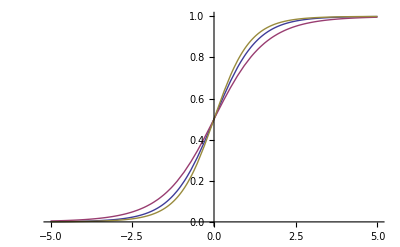

```mathematica
(*  Exact CDF of the TST t-statistic for odd sample sizes Subscript[n, 1]=2m+1 and Subscript[n, 2]=2k+1.
Sample variances are Subscript[σ, 1]^2 and Subscript[σ, 2]^2, Subscript[σ, 1]^2≠Subscript[σ, 2]^2. Ray and Pitman (1961)          *)

ExactTSTCDF[m_,k_,σ1_,σ2_,u_]:=Module[ {a,b,σ,α,β},
  
                                 Subscript[σ, 1]:=σ1;                                           Subscript[σ, 2]:=σ2;

a:=(Subscript[σ, 1]^2(1/(2m+1)+1/(2k+1))/(2m+2k))/(Subscript[σ, 1]^2/(2m+1)+Subscript[σ, 2]^2/(2k+1));                             b:=(Subscript[σ, 2]^2(1/(2m+1)+1/(2k+1))/(2m+2k))/(Subscript[σ, 1]^2/(2m+1)+Subscript[σ, 2]^2/(2k+1));

α[r_]:=((-1)^(m-r-1)(1/(2b)-1/(2a))^r Binomial[m+n-r-2, m-r-1])/((2a)^m(2b)^k(1/(2b)-1/(2a))^(m+k-1)r!);       β[r_]:=((-1)^(k-r-1)(1/(2a)-1/(2b))^r Binomial[m+n-r-2, n-r-1])/((2a)^m(2b)^k(1/(2a)-1/(2b))^(m+k-1)r!);

  ∑_(r=0)^(m-1) (α[r]Gamma[r+1](2a)^(r+1)CDF[StudentTDistribution[2r+2],((2r+2)a)^(1/2)u])+∑_(r=0)^(k-1) (β[r]Gamma[r+1](2b)^(r+1)CDF[StudentTDistribution[2r+2],((2r+2)b)^(1/2)u])
];


Plot[{ExactTSTCDF[1,2,1   ,1.01    ,x],
        ExactTSTCDF[1,2,1   ,0.5,x],
        ExactTSTCDF[1,2,0.5,1   ,x]},{x,-5,5}]
```

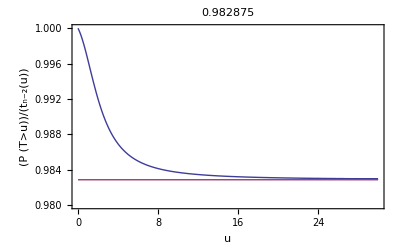

```mathematica
(* Convergency speed in the asymptotic approximation of Zholud D.S. (2013) 
 for the Student two-sample t-test.  Subscript[σ, 1]/Subscript[σ, 2]=1.01.                                    *)

Plot[{(1-ExactTSTCDF[1,2,1,1.01,x])/(1-CDF[StudentTDistribution[6],x]),KgTST[3,5,1,1.01]},
        {x,0,30},
        PlotRange->{Full,{0.98,1}},
        Frame->{{True,False},{True,False}},
        FrameLabel->{u,(P(T>u))/(Subscript[t, n-2][u])},
        PlotLabel->KgTST[3,5,1,1.01]
]
```

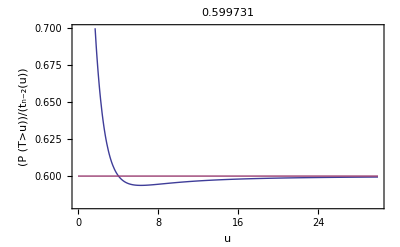

```mathematica
(* Convergency speed in the asymptotic approximation of Zholud D.S. (2013) 
 for the Student two-sample t-test.  Subscript[σ, 1]/Subscript[σ, 2]=0.5.                                  *)

Plot[{(1-ExactTSTCDF[1,2,0.5,1,x])/(1-CDF[StudentTDistribution[6],x]),KgTST[3,5,0.5,1]},
       {x,0,30},
        PlotRange->{Full,{0.58,0.7}},
        Frame->{{True,False},{True,False}},
        FrameLabel->{u,(P(T>u))/(Subscript[t, n-2][u])},
        PlotLabel->KgTST[3,5,0.5,1]]
```

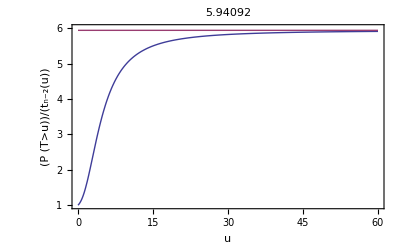

```mathematica
(* Convergency speed in the asymptotic approximation of Zholud D.S. (2013) 
 for the Student two-sample t-test.  Subscript[σ, 1]/Subscript[σ, 2]=2.                                    *)


Plot[{(1-ExactTSTCDF[1,2,1,0.5,x])/(1-CDF[StudentTDistribution[6],x]),KgTST[3,5,1,0.5]},
       {x,0,60},
        PlotRange->{Full,{1,6}},
        Frame->{{True,False},{True,False}},
        FrameLabel->{u,(P(T>u))/(Subscript[t, n-2][u])},
        PlotLabel->KgTST[3,5,1,0.5]]
```